```mathematica
(******(1)******)
(***(a)***)
(*Create three Empirical distributions*)

weighted1=EmpiricalDistribution[{2,1,3,1,1,2}->Range[6]];
weighted2=EmpiricalDistribution[{1,2,1,3,1,1}->Range[6]];
weighted3=EmpiricalDistribution[{2,3,1,1,2,1}->Range[6]];
```

```mathematica
(***(b)***)
(*Compute the probability of the following events:*)(*the sum of the values of the dice is<10*)
Probability[X+Y+Z<10,{X\[Distributed]weighted1,Y\[Distributed]weighted2,Z\[Distributed]weighted3}]
```

203/450

```mathematica
(*the sum of the values of the dice is≥10*)
Probability[X+Y+Z≥10,{X\[Distributed]weighted1,Y\[Distributed]weighted2,Z\[Distributed]weighted3}]
```

247/450

```mathematica
(*the sum of the values of the dice is 12*)
Probability[X+Y+Z==12,{X\[Distributed]weighted1,Y\[Distributed]weighted2,Z\[Distributed]weighted3}]
```

8/75

```mathematica
(*the sum of the values of the dice is 7*)
Probability[X+Y+Z==7,{X\[Distributed]weighted1,Y\[Distributed]weighted2,Z\[Distributed]weighted3}]
```

4/45

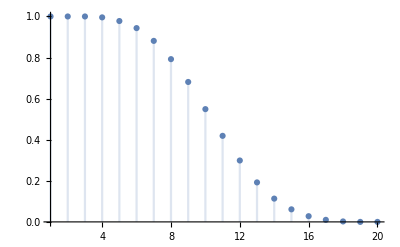

```mathematica
(***(c)***)
(*Use DiscretePlot to get a graph of the distribution of the values of the above
random variables.Get two plots:of X+Y+Z≥n and of X+Y+Z==n.*)
DiscretePlot[Probability[X+Y+Z≥n,{X\[Distributed]weighted1,Y\[Distributed]weighted2,Z\[Distributed]weighted3}],{n,20}]
```

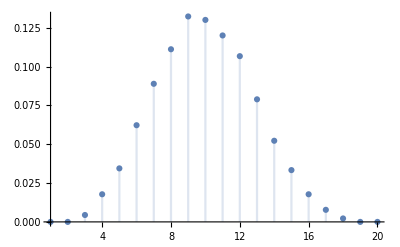

```mathematica
DiscretePlot[Probability[X+Y+Z==n,{X\[Distributed]weighted1,Y\[Distributed]weighted2,Z\[Distributed]weighted3}],{n,20}]
```

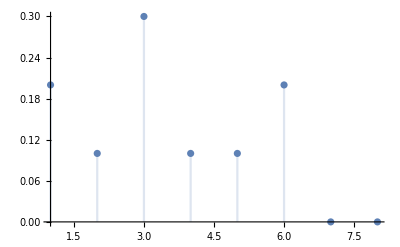

```mathematica
(***(d)***)
(*Use DiscretePlot to get a graph of the weighted1 distribution.*)
DiscretePlot[Probability[X==n,X\[Distributed]weighted1],{n,8}]
```

```mathematica
(***(e)***)
(*Find the mean,the variance and the standard deviation of your weighted1
distribution.*)
Mean[weighted1]
```

17/5

```mathematica
Variance[weighted1]
```

76/25

```mathematica
StandardDeviation[weighted1]
```

(2 √19)/5

```mathematica
(******(2)******)
(*Birthday Problem, probs are .50, .55, .75, .98*)
birthdays[percentage_Real]:=Module[{numPeople=0,curProb=0},
While[curProb<percentage,
numPeople++;
curProb=1-(366!/(366-numPeople)!)/366^numPeople
];
numPeople
]
```

```mathematica
birthdays[.50]
```

23

```mathematica
birthdays[.55]
```

25

```mathematica
birthdays[.75]
```

32

```mathematica
birthdays[.98]
```

53